```mathematica
(*Initialisation - Run first*)
SetEnvironment["OMP_NUM_THREADS"->"8"]
(*Replace the following with the appropriate pathways for your device*)
Import["/Users/questuser/Documents/QuESTlink/Link/QuESTlink.m"] (*QuESTlink load*)
CreateLocalQuESTEnv["/Users/questuser/Documents/Kathryn/quest_link"]; (*Creating QuEST environment*)
Import["/Users/questuser/Documents/Kathryn/Rydberg Custom Gates Custom SWAP.wl"]; (*Configuration File*)
data=Import["/Users/questuser/Documents/Kathryn/SU4Gates9Qubits.csv"]; (*Imported gates from Qiskit*)
userconfig=<|
NQubits-> 9,
QubitLocations->Association[#1->#2&@@@Transpose@{Range[0,8],{{0,0,0},{0,1,0},{1,0,0},{1,1,0},{0,2,0},{1,2,0},{2,0,0},{2,1,0},{2,2,0}}}],
(* blockade radius in μm*)
BlockadeRadius->Sqrt[2],
(*BlockadeRadius->10,*)
(* inter-atomic separation in μm. This will be the unit of the lattice given in qubitLocations *)
UnitLattice->1,
(* T1=τvac/nqubits in μs *)
VacuumLifeTime->4*10^6,
(* the γ noise on theq initialization *)
LeakProbInit->0.007,
(* duration on the initialization *)
DurInit->300,
(* measurement induces atom loss afterward *)
FidMeas-> 100,
DurMeas-> 2*10^4,
(* the increasing chance of atom loss due to measurement, in percent *)
AtomLossMeas-> 0,
(* mostly used in the single qubit noise, unit μs. It's presumed that Subscript[T, 2]^* has been echoed out to Subscript[T, 2] *)
T2->1.49*10^6,
(* leak probability of implementing multi-qubit gates *)
LeakProbCZ-> <|01-> 0.001,11->0.001 |>,
(* Rabi frequency, MHz *)
Ω->1,
(* fidelity of swap operation *)
FidSWAP->99.7
|>;
RydDev=CreateRydbergDevice[userconfig];
RydDev[InitLocations]
(*Defining QuEST's Rydberg Blockade Check in a permanent function such that it can be used without constantly editing the code*)
qubitLocs=userconfig[QubitLocations];
distloc[q1_,q2_]:=Norm[qubitLocs[q1]-qubitLocs[q2],2]*userconfig[UnitLattice];
blockadeCheck[q_List]:=And@@((distloc@@#<= userconfig[BlockadeRadius])&/@Subsets[Flatten[q],{2}]);
RydDev[Gates][[All,1]]
```

-Graphics3D-

{Init_q$_Integer,Wait_qubits$__[dur$_]/;Complement[Flatten[{qubits$}],Range[0,userconfig[NQubits]-1]]==={},M_q$_Integer,SRot_q$_Integer[ϕ$_,Δ$_,tg$_],H_q$_Integer,Rx_q$_Integer[θ$_],Ry_q$_Integer[θ$_],Rz_q$_Integer[θ$_],SWAPDCG_(q1$_Integer,q2$_Integer),SWAPDCH_(q1$_Integer,q2$_Integer),InstaSWAP_(q1_,q2_),SWAPLoc_(q1$_Integer,q2$_Integer),ShiftLoc_q$__[v$_]/;LegitShift[Flatten[{q$}],qubitLocs$1402545,v$],CZ_(p$_Integer,q$_Integer)[ϕ$_]/;blockadeCheck$1402545[{p$,q$}],CZG_(p$_Integer,q$_Integer)/;blockadeCheck$1402545[{p$,q$}],CZH_(p$_Integer,q$_Integer)/;blockadeCheck$1402545[{p$,q$}],CCZ_(i$_,j$_,k$_)/;blockadeCheck$1402545[{i$,j$}]/;blockadeCheck$1402545[{j$,k$}]/;blockadeCheck$1402545[{k$,i$}],C_c$_[Z_t$__]/;blockadeCheck$1402545[{c$,t$}],C_c$_[Z_t$__[θ$_]]/;blockadeCheck$1402545[{c$,t$}],C_c$__[Z_t$_]/;blockadeCheck$1402545[{c$,t$}],C_c$__[Z_t$_[θ$_]]}

```mathematica
ExtractCircuit[InsertCircuitNoise[{Subscript[CZG, 0,1]},RydDev,ReplaceAliases->True]]
```

{UNonNorm_(0,1)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[0.],Deph_1[0.],Deph_2[4.36241×10^-7],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[4.36241×10^-7],Deph_7[4.36241×10^-7],Deph_8[4.36241×10^-7]}

```mathematica
Fraction[a_,b_]:=a/b
KetList[NQ_]:=Table[i,{i,0,2^NQ-1,1}]
```

```mathematica
(*Fully Translate Qiskit output into QuEST format, A-2-A Procedure, Pelegri CZ*)
MoveTime=500;
SU4GateGINSTA[DataSet_,q1_,q2_]:=Table[
a=Reverse[IntegerPart[ToExpression[StringSplit[StringTrim[StringSplit[DataSet[[i]],", ["][[2]],"]"],","]]]];b=If[Length[a]==1,StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],StringSplit[StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],"C"][[1]]];
c=StringReplace[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[3]]],"]]"],{"("->"[",")"->"]"}];
c=If[StringContainsQ[c,"e"],d=StringSplit[c,"e"];ToExpression[d[[1]]]*10^ToExpression[d[[2]]],ToExpression[c]];
a=ReplaceAll[a,{0->q1,1->q2}];
If[Length[a]==2,If[StringContainsQ[b,"SWAP"],Subscript[ToExpression[InstaSWAP], a[[1]],a[[2]]],Subscript[CZG, a[[2]],a[[1]]]],If[c==={},Subscript[ToExpression[b], a[[1]]],Subscript[ToExpression[b], a[[1]]][c]]],{i,1,Length[DataSet]}]
(*Fully Translate Qiskit output into QuEST format, A-2-A Procedure, Levine CZ*)
SU4GateHINSTA[DataSet_,q1_,q2_]:=Table[
a=Reverse[IntegerPart[ToExpression[StringSplit[StringTrim[StringSplit[DataSet[[i]],", ["][[2]],"]"],","]]]];b=If[Length[a]==1,StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],StringSplit[StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],"C"][[1]]];
c=StringReplace[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[3]]],"]]"],{"("->"[",")"->"]"}];
c=If[StringContainsQ[c,"e"],d=StringSplit[c,"e"];ToExpression[d[[1]]]*10^ToExpression[d[[2]]],ToExpression[c]];
a=ReplaceAll[a,{0->q1,1->q2}];
If[Length[a]==2,If[StringContainsQ[b,"SWAP"],Subscript[ToExpression[InstaSWAP], a[[1]],a[[2]]],Subscript[CZH, a[[2]],a[[1]]]],If[c==={},Subscript[ToExpression[b], a[[1]]],Subscript[ToExpression[b], a[[1]]][c]]],{i,1,Length[DataSet]}]
(*Fully Translate Qiskit output into QuEST format, SWAP Procedure, Pelegri CZ*)
SU4GateGDC[DataSet_,q1_,q2_]:=Table[
a=Reverse[IntegerPart[ToExpression[StringSplit[StringTrim[StringSplit[DataSet[[i]],", ["][[2]],"]"],","]]]];b=If[Length[a]==1,StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],StringSplit[StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],"C"][[1]]];
c=StringReplace[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[3]]],"]]"],{"("->"[",")"->"]"}];
c=If[StringContainsQ[c,"e"],d=StringSplit[c,"e"];ToExpression[d[[1]]]*10^ToExpression[d[[2]]],ToExpression[c]];
a=ReplaceAll[a,{0->q1,1->q2}];
If[Length[a]==2,If[StringContainsQ[b,"SWAP"],Subscript[ToExpression[SWAPDCG], a[[1]],a[[2]]],Subscript[CZG, a[[2]],a[[1]]]],If[c==={},Subscript[ToExpression[b], a[[1]]],Subscript[ToExpression[b], a[[1]]][c]]],{i,1,Length[DataSet]}]
(*Fully Translate Qiskit output into QuEST format, SWAP Procedure, Levine CZ*)
SU4GateHDC[DataSet_,q1_,q2_]:=Table[
a=Reverse[IntegerPart[ToExpression[StringSplit[StringTrim[StringSplit[DataSet[[i]],", ["][[2]],"]"],","]]]];b=If[Length[a]==1,StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],StringSplit[StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],"C"][[1]]];
c=StringReplace[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[3]]],"]]"],{"("->"[",")"->"]"}];
c=If[StringContainsQ[c,"e"],d=StringSplit[c,"e"];ToExpression[d[[1]]]*10^ToExpression[d[[2]]],ToExpression[c]];
a=ReplaceAll[a,{0->q1,1->q2}];
If[Length[a]==2,If[StringContainsQ[b,"SWAP"],Subscript[ToExpression[SWAPDCH], a[[1]],a[[2]]],Subscript[CZH, a[[2]],a[[1]]]],If[c==={},Subscript[ToExpression[b], a[[1]]],Subscript[ToExpression[b], a[[1]]][c]]],{i,1,Length[DataSet]}]
(*Fully Translate Qiskit output into QuEST format, Movement Procedure, Pelegri CZ*)
SU4GateGMove[DataSet_,q1_,q2_]:=Table[a=Reverse[IntegerPart[ToExpression[StringSplit[StringTrim[StringSplit[DataSet[[i]],", ["][[2]],"]"],","]]]];
b=If[Length[a]==1,StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],StringSplit[StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],"C"][[1]]];
c=StringReplace[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[3]]],"]]"],{"("->"[",")"->"]"}];
c=If[StringContainsQ[c,"e"],d=StringSplit[c,"e"];
ToExpression[d[[1]]]*10^ToExpression[d[[2]]],ToExpression[c]];
a=ReplaceAll[a,{0->q1,1->q2}];
If[Length[a]==2,If[StringContainsQ[b,"SWAP"],Subscript[ToExpression[SWAP],a[[1]],a[[2]]],{Subscript[CZG,a[[2]],a[[1]]]}],If[c==={},Subscript[ToExpression[b],a[[1]]],Subscript[ToExpression[b],a[[1]]][c]]],{i,1,Length[DataSet]}]
(*Fully Translate Qiskit output into QuEST format, Movement Procedure, Levine CZ*)
SU4GateHMove[DataSet_,q1_,q2_]:=Table[a=Reverse[IntegerPart[ToExpression[StringSplit[StringTrim[StringSplit[DataSet[[i]],", ["][[2]],"]"],","]]]];
b=If[Length[a]==1,StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],StringSplit[StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],"C"][[1]]];
c=StringReplace[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[3]]],"]]"],{"("->"[",")"->"]"}];
c=If[StringContainsQ[c,"e"],d=StringSplit[c,"e"];
ToExpression[d[[1]]]*10^ToExpression[d[[2]]],ToExpression[c]];
a=ReplaceAll[a,{0->q1,1->q2}];
If[Length[a]==2,If[StringContainsQ[b,"SWAP"],Subscript[ToExpression[SWAP],a[[1]],a[[2]]],{Subscript[CZH,a[[2]],a[[1]]]}],If[c==={},Subscript[ToExpression[b],a[[1]]],Subscript[ToExpression[b],a[[1]]][c]]],{i,1,Length[DataSet]}]
(*SU4Gate[data[[400;;1000]][[112]],0,1]*)
```

```mathematica
(*Generate a list of random permutations of NQ qubits*)
NRandQbits[NQ_]:=RandomSample[Range[0,NQ-1],NQ]

(*Compute the probability of getting a heavy output of the model circuit from the noisy circuit THIS STILL AIN'T RIGHT*)
CheckHeavyOutputProb[PoutcomesIMPLEMENTED_,PoutcomesMODEL_]:=Pick[PoutcomesIMPLEMENTED,Table[If[PoutcomesMODEL[[i]]>=Median[PoutcomesMODEL],True,False],{i,1,Length[PoutcomesMODEL]}]];
```

```mathematica
(*Generate a layer of gates for building a QV circuit*)
QVLayerGA2A[DataSet_,NQ_,RQs_,i_]:=Table[If[blockadeCheck[{RQs[[n]],RQs[[n+1]]}],LayerCirc=SU4GateGINSTA[DataSet[[n+i]],RQs[[n]],RQs[[n+1]]],LayerCirc=Flatten[Join[Join[{Subscript[InstaSWAP, RQs[[n+1]],3]},SU4GateGINSTA[DataSet[[n+i]],RQs[[n]],3]],{Subscript[InstaSWAP, RQs[[n+1]],3]}]]]; LayerCirc,{n,1,2*Quotient[NQ,2],2}];

QVLayerGSWAP[DataSet_,NQ_,RQs_,i_]:=Table[If[blockadeCheck[{RQs[[n]],RQs[[n+1]]}],LayerCirc=SU4GateGDC[DataSet[[n+i]],RQs[[n]],RQs[[n+1]]],LayerCirc=Flatten[Join[Join[{Subscript[SWAPDCG, RQs[[n+1]],3]},SU4GateGDC[DataSet[[n+i]],RQs[[n]],3]],{Subscript[SWAPDCG, RQs[[n+1]],3]}]]]; LayerCirc,{n,1,2*Quotient[NQ,2],2}];

QVLayerGMove[DataSet_,NQ_,RQs_,i_]:=Table[LayerCirc=Join[{Subscript[Wait, Range[0,userconfig[NQubits]-1]][500]},SU4GateGMove[DataSet[[n+i]],RQs[[n]],RQs[[n+1]]]],{n,1,2*Quotient[NQ,2],2}];

QVLayerHA2A[DataSet_,NQ_,RQs_,i_]:=Table[If[blockadeCheck[{RQs[[n]],RQs[[n+1]]}],LayerCirc=SU4GateHINSTA[DataSet[[n+i]],RQs[[n]],RQs[[n+1]]],LayerCirc=Flatten[Join[Join[{Subscript[InstaSWAP, RQs[[n+1]],3]},SU4GateHINSTA[DataSet[[n+i]],RQs[[n]],3]],{Subscript[InstaSWAP, RQs[[n+1]],3]}]]]; LayerCirc,{n,1,2*Quotient[NQ,2],2}];

QVLayerHSWAP[DataSet_,NQ_,RQs_,i_]:=Table[If[blockadeCheck[{RQs[[n]],RQs[[n+1]]}],LayerCirc=SU4GateHDC[DataSet[[n+i]],RQs[[n]],RQs[[n+1]]],LayerCirc=Flatten[Join[Join[{Subscript[SWAPDCH, RQs[[n+1]],3]},SU4GateHDC[DataSet[[n+i]],RQs[[n]],3]],{Subscript[SWAPDCH, RQs[[n+1]],3]}]]]; LayerCirc,{n,1,2*Quotient[NQ,2],2}];

QVLayerHMove[DataSet_,NQ_,RQs_,i_]:=Table[LayerCirc=Join[{Subscript[Wait, Range[0,userconfig[NQubits]-1]][500]},SU4GateHMove[DataSet[[n+i]],RQs[[n]],RQs[[n+1]]]],{n,1,2*Quotient[NQ,2],2}];
```

```mathematica
ExtractCircuit[InsertCircuitNoise[{Subscript[Wait, Range[0,userconfig[NQubits]-1]][500]},RydDev]]
```

{Deph_0[0.000167757],Deph_1[0.000167757],Deph_2[0.000167757],Deph_3[0.000167757],Deph_4[0.000167757],Deph_5[0.000167757],Deph_6[0.000167757],Deph_7[0.000167757],Deph_8[0.000167757],Deph_0[0.],Deph_1[0.],Deph_2[0.],Deph_3[0.],Deph_4[0.],Deph_5[0.],Deph_6[0.],Deph_7[0.],Deph_8[0.]}

```mathematica
(*Generate initialisation layer of circuit*)
InitCirc[Reg_,MaxNQ_]:=Table[Subscript[Init, b],{b,0,MaxNQ-1,1}]
```

```mathematica
(*Generate circuit of m=d layers of SU(4) gates*)
QVCirc[DataSet_,NQ_,ConnectivityRule_]:=Table[RQS=NRandQbits[NQ];Layer=Which[StringContainsQ[ConnectivityRule,"GA2A"],QVLayerGA2A[DataSet,NQ,RQS,i],StringContainsQ[ConnectivityRule,"GSWAP"],QVLayerGSWAP[DataSet,NQ,RQS,i],StringContainsQ[ConnectivityRule,"GMove"],QVLayerGMove[DataSet,NQ,RQS,i],StringContainsQ[ConnectivityRule,"HA2A"],QVLayerHA2A[DataSet,NQ,RQS,i],StringContainsQ[ConnectivityRule,"HSWAP"],QVLayerHSWAP[DataSet,NQ,RQS,i],StringContainsQ[ConnectivityRule,"HMove"],QVLayerHMove[DataSet,NQ,RQS,i]];
(*Print["# Qubits, ",NQ," # Gates per Layer, ",Length[Layer]]*);Flatten[Layer],{i,0,NQ-1,1}]
```

```mathematica
(*Generating and applying the circuits to a register and getting the probability of a heavy output*)
QVProcedure[DataSet_,NQ_, MaxNQ_,NReps_,Reg_,ConnectivityRule_]:=Table[
Circ1=QVCirc[DataSet[[NQ*Quotient[NQ,2]*Rep+1;;NQ*Quotient[NQ,2]*(Rep+1)]],NQ,ConnectivityRule];
Initialisation=InitCirc[Reg,MaxNQ];
InitCircuit=Flatten[Join[Initialisation,Circ1]];
CircNoisy=ExtractCircuit[InsertCircuitNoise[InitCircuit,RydDev,ReplaceAliases->True]];
CircModel=ExtractCircuit[GetCircuitSchedule[Circ1,RydDev,ReplaceAliases->True]];
SetQuregMatrix[Reg,RandomMixState[MaxNQ]];
ApplyCircuit[Reg,CircNoisy];
PoutcomesNoisy=CalcProbOfAllOutcomes[Reg,Range[0,NQ-1]];
(*Print[PoutcomesNoisy];*)
InitZeroState[Reg];
(*Print[DrawCircuit[CircModel]];*)
ApplyCircuit[Reg,CircModel];
PoutcomesModel=CalcProbOfAllOutcomes[Reg,Range[0,NQ-1]];
PNoLoss=Total[PoutcomesNoisy];
PoutcomesNoisyRen=PoutcomesNoisy/PNoLoss;
(*Print[NQ, " Model Outcomes Probabilities ",PoutcomesModel," Noisy Outcome Probabilities ",PoutcomesNoisy];*)
HeavyOutputs=CheckHeavyOutputProb[PoutcomesNoisy,PoutcomesModel];
HeavyOutputsRen=CheckHeavyOutputProb[PoutcomesNoisyRen,PoutcomesModel];
{Total[HeavyOutputs],Total[HeavyOutputsRen],1-PNoLoss},{Rep,0,NReps-1,1}]


(*Put everything together and get a value for Quantum Volume*)
QVCalc[DataSet_,MaxNQ_,NReps_,ConnectivityRule_]:=Table[ρ=CreateDensityQureg[MaxNQ];
HOP=QVProcedure[DSSplice=DataSet[[(Total[Table[a*Quotient[a,2],{a,0,NQ-1}]]*NReps)+1 ;;Total[Table[a*Quotient[a,2],{a,0,NQ}]*NReps]]],NQ,MaxNQ,NReps,ρ,ConnectivityRule];
DestroyAllQuregs[];
MHOP=Mean[HOP[[All,1]]];
MHOPRen=Mean[HOP[[All,2]]];
MPLoss=Mean[HOP[[All,3]]];
σPLoss=StandardDeviation[HOP[[All,3]]]/Sqrt[NReps-1];
σ=StandardDeviation[HOP[[All,1]]]/Sqrt[NReps-1];
σRen=StandardDeviation[HOP[[All,2]]]/Sqrt[NReps-1];
If[ Re[(MHOP-2σ)]>2/3,VQ=2^NQ,VQ=0];
If[ Re[(MHOPRen-2σRen)]>2/3,VQRen=2^NQ,VQRen=0];
Print[{"Layer",NQ,VQ,VQRen}];
{{NQ,MHOP,2σ},{NQ,MHOPRen,2σRen},{NQ,MPLoss,σPLoss}}
,{NQ,2,MaxNQ,1}];


GA2AQV=QVCalc[data,9,200,"GA2A"]
GSWAPQV=QVCalc[data,9,200,"GSWAP"]
HA2AQV=QVCalc[data,9,200,"HA2A"]
HSWAPQV=QVCalc[data,9,200,"HSWAP"]

(*GMoveQV=QVCalc[data,9,200,"GMove"]*)
(*HMoveQV=QVCalc[data,9,200,"HMove"]*)
DestroyAllQuregs[];
```

{Layer,2,4,4}

{Layer,3,8,8}

{Layer,4,16,16}

{Layer,5,32,32}

{Layer,6,64,64}

{Layer,7,128,128}

{Layer,8,256,256}

{Layer,9,0,512}

{{{2,0.740116,0.0126374},{2,0.796491,0.0136151},{2,0.0707611,0.0000949655}},{{3,0.780853,0.0112328},{3,0.84474,0.0121506},{3,0.0756293,0.00011586}},{{4,0.757217,0.00612833},{4,0.840219,0.00681093},{4,0.0987777,0.000149903}},{{5,0.761395,0.00472409},{5,0.853493,0.0053153},{5,0.107898,0.000157762}},{{6,0.724914,0.00307074},{6,0.84655,0.00362169},{6,0.143672,0.000206461}},{{7,0.720205,0.00228348},{7,0.854002,0.00266374},{7,0.156673,0.000202027}},{{8,0.672465,0.00149906},{8,0.843509,0.00181385},{8,0.202779,0.0001844}},{{9,0.660642,0.00113658},{9,0.845687,0.00142245},{9,0.218808,0.000215995}}}

{Layer,2,4,4}

{Layer,3,8,8}

{Layer,4,16,16}

{Layer,5,32,32}

{Layer,6,64,64}

{Layer,7,0,128}

{Layer,8,0,256}

{Layer,9,0,512}

{{{2,0.738544,0.0130813},{2,0.794683,0.0140873},{2,0.0706297,0.0000971052}},{{3,0.792221,0.0116047},{3,0.857117,0.0125704},{3,0.0757037,0.000117025}},{{4,0.751957,0.00694481},{4,0.834264,0.00764543},{4,0.0986858,0.000162739}},{{5,0.746222,0.00467712},{5,0.85248,0.00522621},{5,0.124627,0.000683566}},{{6,0.688279,0.00382703},{6,0.843643,0.00400341},{6,0.184222,0.000925285}},{{7,0.661792,0.00295608},{7,0.849236,0.00274684},{7,0.220763,0.00104192}},{{8,0.588049,0.00251257},{8,0.837713,0.00188879},{8,0.298029,0.00127706}},{{9,0.557702,0.00251194},{9,0.838175,0.0014502},{9,0.334651,0.00131161}}}

{Layer,2,4,4}

{Layer,3,8,8}

{Layer,4,16,16}

{Layer,5,32,32}

{Layer,6,64,64}

{Layer,7,128,128}

{Layer,8,256,256}

{Layer,9,512,512}

{{{2,0.739504,0.0125001},{2,0.792213,0.0133904},{2,0.0665345,0.0000411608}},{{3,0.788116,0.0112311},{3,0.846819,0.0120686},{3,0.0693207,0.0000493094}},{{4,0.766353,0.00663187},{4,0.835246,0.00721693},{4,0.0824872,0.0000717361}},{{5,0.779174,0.00502263},{5,0.853968,0.00552081},{5,0.087579,0.0000728685}},{{6,0.754007,0.00345171},{6,0.845591,0.0038497},{6,0.108312,0.0000805642}},{{7,0.753675,0.00249883},{7,0.852359,0.00283482},{7,0.115775,0.0000849364}},{{8,0.718455,0.00168053},{8,0.838566,0.00197321},{8,0.143231,0.0000919158}},{{9,0.710527,0.00121394},{9,0.838756,0.00141654},{9,0.152881,0.0000913182}}}

{Layer,2,4,4}

{Layer,3,8,8}

{Layer,4,16,16}

{Layer,5,32,32}

{Layer,6,64,64}

{Layer,7,128,128}

{Layer,8,0,256}

{Layer,9,0,512}

{{{2,0.73602,0.0132171},{2,0.788499,0.0141599},{2,0.0665546,0.0000413264}},{{3,0.792501,0.0112423},{3,0.851514,0.0120737},{3,0.0693089,0.0000488048}},{{4,0.770184,0.00669357},{4,0.839509,0.00729139},{4,0.0825786,0.0000660969}},{{5,0.768632,0.00540908},{5,0.852656,0.00591322},{5,0.0985578,0.000423606}},{{6,0.729615,0.00366042},{6,0.839767,0.00401995},{6,0.131184,0.00057193}},{{7,0.708235,0.00325783},{7,0.83909,0.00337701},{7,0.156007,0.000622148}},{{8,0.656421,0.00251612},{8,0.82246,0.00213191},{8,0.201954,0.000824317}},{{9,0.632409,0.00256968},{9,0.816929,0.00218398},{9,0.225965,0.000812656}}}

```mathematica
GA2AQV={{{2,0.7401162361932938,0.012637402938430044},{2,0.7964910548441765,0.013615081829584806},{2,0.07076106272829308,0.00009496551045323869}},{{3,0.7808532734596401,0.01123275654433871},{3,0.8447396543799234,0.01215058728845331},{3,0.07562931638415364,0.00011586005035170743}},{{4,0.7572166665746672,0.0061283295238743615},{4,0.8402190512308235,0.006810933798660399},{4,0.09877769604894619,0.00014990333455840776}},{{5,0.7613954507678449,0.004724091434035621},{5,0.8534934972859408,0.005315298762662819},{5,0.10789774584511402,0.0001577619051451092}},{{6,0.72491413953848,0.003070743211518393},{6,0.8465497326979022,0.003621691294356924},{6,0.14367176628953648,0.00020646140845817672}},{{7,0.7202052146330551,0.0022834759574453037},{7,0.8540021880281137,0.0026637373916687302},{7,0.1566725842572415,0.0002020269766782662}},{{8,0.6724650819726615,0.001499064227642442},{8,0.8435092994161215,0.0018138549412841302},{8,0.20277949962408917,0.00018439999069727174}},{{9,0.6606416280853489,0.001136576917978405},{9,0.8456871478911799,0.0014224486170797013},{9,0.21880755817804454,0.0002159953763090035}}};
GSWAPQV={{{2,0.7385437654523592,0.013081332204174172},{2,0.7946826680306497,0.014087291794305595},{2,0.07062967951052807,0.00009710520136629708}},{{3,0.792220587029426,0.011604728416065776},{3,0.8571167974225081,0.012570373403594699},{3,0.07570367140411148,0.0001170247850895079}},{{4,0.7519574951146256,0.006944807601624424},{4,0.8342643709643381,0.00764543034983276},{4,0.09868576301008326,0.00016273872766698808}},{{5,0.7462217639480777,0.004677118329632618},{5,0.8524795227539326,0.005226213989646866},{5,0.1246270996856866,0.0006835656642485405}},{{6,0.6882794295428356,0.0038270291871549526},{6,0.8436429455565759,0.00400340894357009},{6,0.18422231115955548,0.0009252852590566622}},{{7,0.6617920439380494,0.0029560779250699925},{7,0.8492363741796725,0.002746844857571925},{7,0.22076343555945882,0.0010419163543244619}},{{8,0.5880493716574564,0.0025125739908954787},{8,0.837713235184869,0.0018887916406530524},{8,0.29802859662043363,0.0012770621300877366}},{{9,0.5577024715963084,0.0025119358203032588},{9,0.8381753384189037,0.0014502033575082755},{9,0.33465061220089365,0.001311608040016103}}};
GMoveQV={{{2,0.7440380415501708,0.012172850527593109},{2,0.8006176279492385,0.013111185984753249},{2,0.07065474599058007,0.00009590540657175703}},{{3,0.7863161183504753,0.011774137581726485},{3,0.8505988167924314,0.012741505270513},{3,0.07556875373332143,0.00011247385820191145}},{{4,0.7533247359847417,0.0060055181084541056},{4,0.8359643888965307,0.006698114563627852},{4,0.09883834150231889,0.00015123410917306732}},{{5,0.761785302497577,0.004653251566168227},{5,0.8537090128505596,0.005207764868202274},{5,0.10767499115669789,0.00016442019695776222}},{{6,0.7201711296366924,0.003109657286851188},{6,0.8407989394359325,0.003597029556830769},{6,0.14347167144000414,0.0001783466984564355}},{{7,0.7152438830873794,0.0025950939147109005},{7,0.8479296775042837,0.003083464224237825},{7,0.1564764477574725,0.00019225243044493392}},{{8,0.6651269018155499,0.00151004759511243},{8,0.8339920138264345,0.0018149529005010937},{8,0.20248121971639935,0.00020307440784029452}},{{9,0.6499782712994356,0.0011836383331234846},{9,0.8323090629375691,0.0014467527734972339},{9,0.21906658886883373,0.00020495045478025945}}};
```

{{{2,0.738544,0.0130813},{2,0.794683,0.0140873},{2,0.0706297,0.0000971052}},{{3,0.792221,0.0116047},{3,0.857117,0.0125704},{3,0.0757037,0.000117025}},{{4,0.751957,0.00694481},{4,0.834264,0.00764543},{4,0.0986858,0.000162739}},{{5,0.746222,0.00467712},{5,0.85248,0.00522621},{5,0.124627,0.000683566}},{{6,0.688279,0.00382703},{6,0.843643,0.00400341},{6,0.184222,0.000925285}},{{7,0.661792,0.00295608},{7,0.849236,0.00274684},{7,0.220763,0.00104192}},{{8,0.588049,0.00251257},{8,0.837713,0.00188879},{8,0.298029,0.00127706}},{{9,0.557702,0.00251194},{9,0.838175,0.0014502},{9,0.334651,0.00131161}}}

```mathematica
HA2AQV={{{2,0.7395038025303511,0.012500061078456299},{2,0.7922130585192657,0.013390356451782562},{2,0.06653445736765941,0.00004116083303142296}},{{3,0.7881156991849168,0.011231088777734747},{3,0.8468187524157625,0.012068634192720633},{3,0.06932065127188052,0.000049309368314147395}},{{4,0.7663525092702852,0.006631871438140983},{4,0.8352455143329968,0.007216925190795983},{4,0.08248718373257713,0.0000717360944454337}},{{5,0.7791736297431351,0.005022632035766057},{5,0.8539682459559107,0.005520813433958581},{5,0.08757901691434399,0.0000728685350031681}},{{6,0.7540071108751444,0.003451705802379213},{6,0.8455912243462226,0.0038496973556442393},{6,0.10831210207984326,0.00008056417971484877}},{{7,0.7536748378987533,0.0024988267216910173},{7,0.8523587080188699,0.0028348181296783967},{7,0.11577515158388982,0.00008493642105560209}},{{8,0.7184553407102616,0.0016805295383468073},{8,0.8385661993208692,0.0019732099697808017},{8,0.14323121417751422,0.0000919157607595595}},{{9,0.710526533692656,0.0012139358678333516},{9,0.8387560496233778,0.0014165360179863135},{9,0.1528810014774544,0.00009131820998315612}}};
HSWAPQV={{{2,0.736020408665725,0.013217082052261882},{2,0.7884992192251901,0.014159858046417628},{2,0.06655464818471435,0.00004132643149559318}},{{3,0.7925012682675612,0.011242323438140155},{3,0.8515141775619601,0.012073746720710704},{3,0.06930885447260536,0.0000488047947868445}},{{4,0.7701844200706783,0.006693566396881166},{4,0.8395085735500207,0.007291390207184254},{4,0.08257863256721062,0.00006609690507736421}},{{5,0.7686319719780605,0.005409076905819809},{5,0.852656189492939,0.0059132208066803235},{5,0.0985578434486435,0.00042360551418593853}},{{6,0.729614513592723,0.0036604179249481498},{6,0.8397674942468472,0.004019953634772593},{6,0.1311835125135085,0.0005719299448629759}},{{7,0.708234794061019,0.003257834225310854},{7,0.8390902090067585,0.0033770051038747675},{7,0.15600710232801784,0.0006221481065766971}},{{8,0.6564212706558518,0.0025161179634201622},{8,0.822460339580069,0.002131913814529407},{8,0.2019544491915967,0.0008243169953289579}},{{9,0.6324088046748761,0.0025696795267036872},{9,0.8169286705310489,0.002183978610386512},{9,0.22596537187801538,0.0008126562503135459}}};
HMoveQV={{{2,0.7358714737977795,0.012625439474830056},{2,0.7883006961701807,0.013525986853384625},{2,0.06650788607588057,0.00004003946807275312}},{{3,0.7903584792299446,0.012186801658316822},{3,0.8492030631160659,0.013087745239180907},{3,0.06929777458938952,0.000050824880739423185}},{{4,0.7673193360848998,0.0064120300719689135},{4,0.8362926479670287,0.006986656579598332},{4,0.08247495644567934,0.00006875848884939714}},{{5,0.7770959051662706,0.005170008961624145},{5,0.8516941750292483,0.0056814517370627066},{5,0.08758244938633751,0.00007878220461476464}},{{6,0.7481693845138571,0.0035216165268179365},{6,0.8388747096296767,0.003956633195585442},{6,0.108124592524178,0.00008414189749192513}},{{7,0.7461912520289721,0.002543564408040839},{7,0.8441014698590927,0.0028579878243141232},{7,0.11599611340668375,0.00008555557781036946}},{{8,0.7087474297285451,0.001723351001510946},{8,0.8272163150284476,0.001999963459757121},{8,0.14321443706531967,0.00008873875109147182}},{{9,0.6996986801451152,0.0012505916297016805},{9,0.8259689103605765,0.001460579223412425},{9,0.15287578589147738,0.00008678819619880523}}};
```

```mathematica
ErrorBars[Data_]:=Table[{Data[[i,1]],Data[[i,2]]±Data[[i,3]]},{i,1,Length[Data]}]
ErrorBarsLoss[Data_]:=Table[{Data[[i,1]],Data[[i,2]]±2Data[[i,3]]},{i,1,Length[Data]}]
```

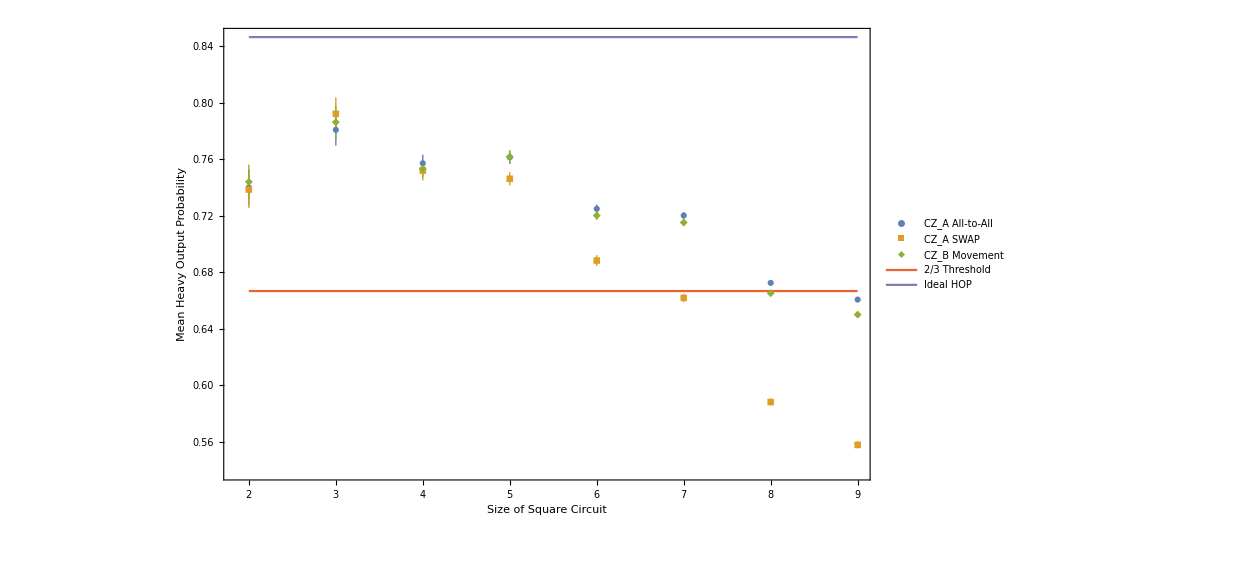

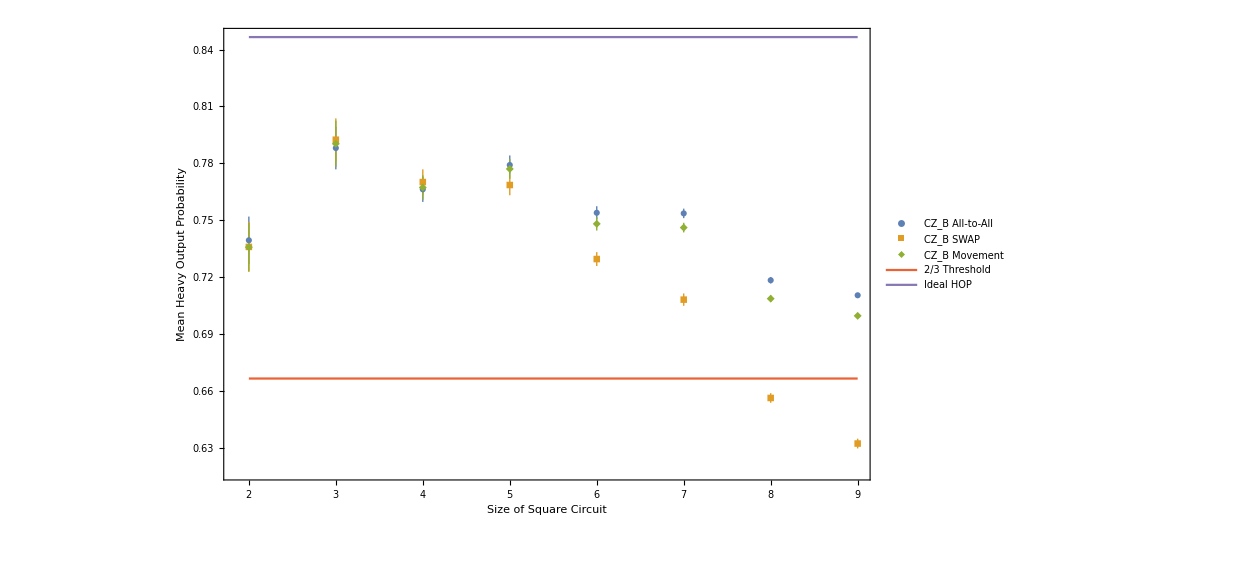

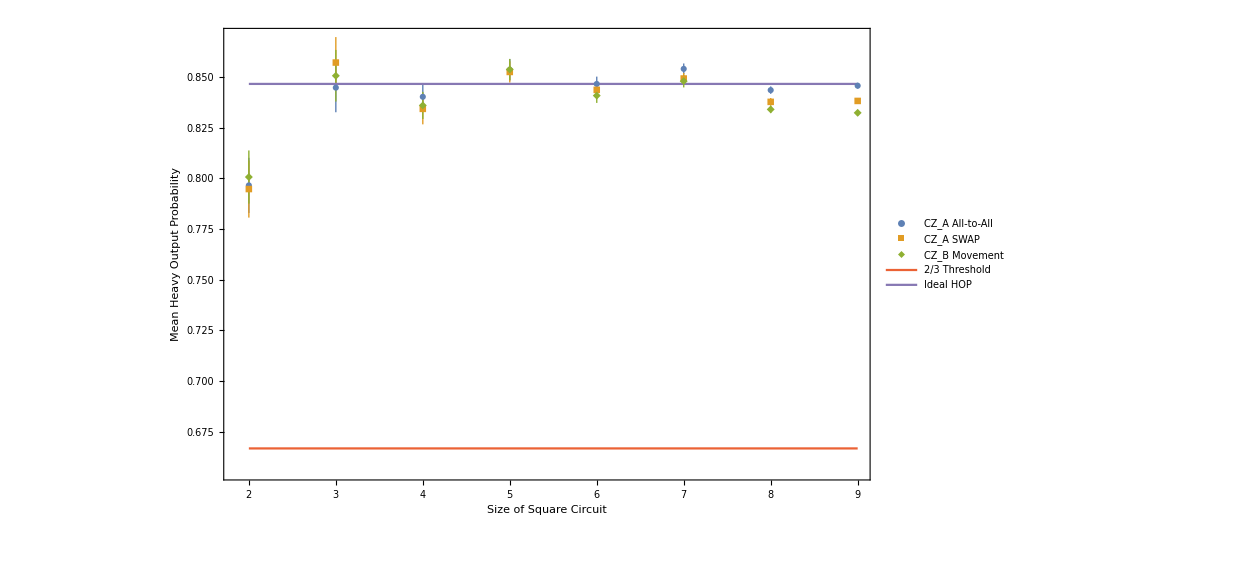

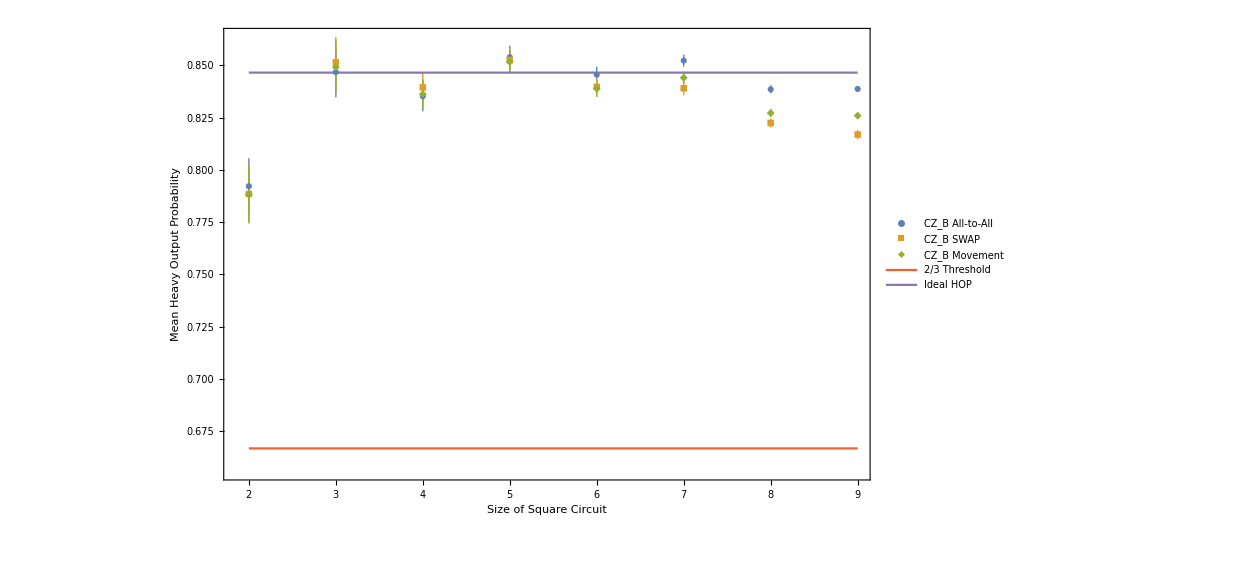

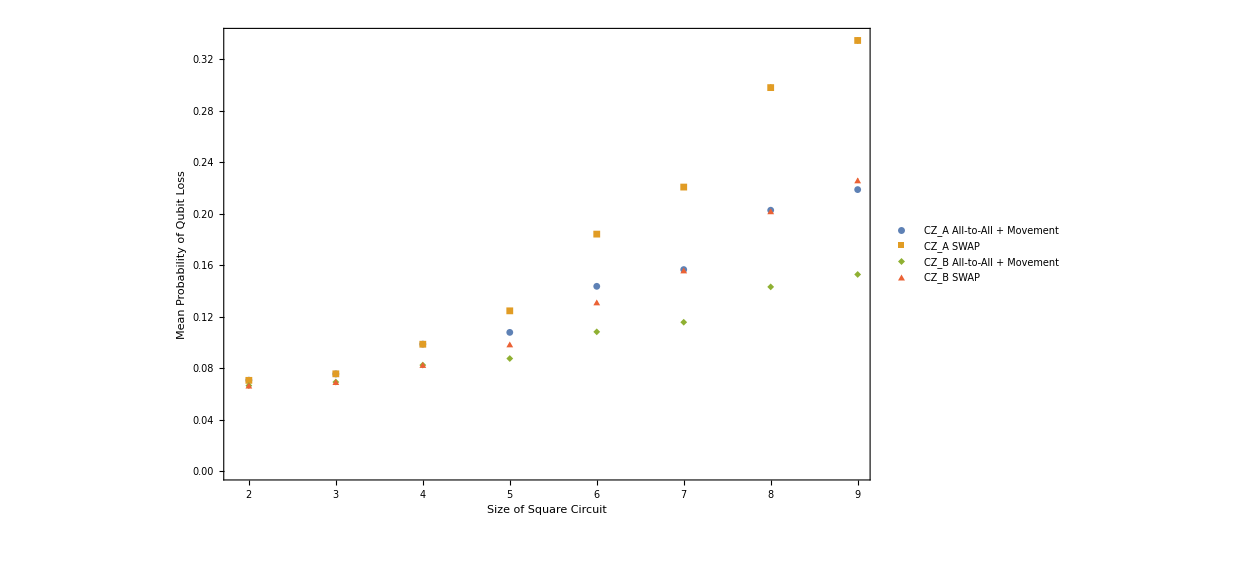

ListLinePlot[{{{2,0.790791±0.0135248},{3,0.848959±0.0119877},{4,0.838436±0.00702298},{5,0.856675±0.0053932},{6,0.850073±0.0038278},{7,0.85422±0.00281338},{8,0.844107±0.00199746},{9,0.845441±0.00139288}},{{2,0.792255±0.0141166},{3,0.847278±0.0124506},{4,0.831176±0.00731335},{5,0.859684±0.00575786},{6,0.846±0.00433786},{7,0.849931±0.00382282},{8,0.837428±0.00375029},{9,0.83543±0.00349307}},{{2,0.797108,0.0128986},{3,0.851692,0.0124526},{4,0.837986,0.00759597},{5,0.855545,0.00517676},{6,0.843309,0.00339957},{7,0.846971,0.00304184},{8,0.832896,0.00208175},{9,0.831794,0.00152376}},{{2,0.789541±0.013737},{3,0.8496±0.0120126},{4,0.834851±0.00702776},{5,0.855517±0.00566381},{6,0.844564±0.00408157},{7,0.851169±0.00298564},{8,0.837976±0.00215053},{9,0.837825±0.0015128}},{{2,0.790255±0.0138441},{3,0.848666±0.0122158},{4,0.838279±0.00670451},{5,0.846128±0.00585462},{6,0.84643±0.00405432},{7,0.839087±0.00371424},{8,0.826037±0.00301181},{9,0.81664±0.00315689}},{{2,0.790255,0.0138441},{3,0.848666,0.0122158},{4,0.838279,0.00670451},{5,0.846128,0.00585462},{6,0.84643,0.00405432},{7,0.839087,0.00371424},{8,0.826037,0.00301181},{9,0.81664,0.00315689}},{{2,2/3},{3,2/3},{4,2/3},{5,2/3},{6,2/3},{7,2/3},{8,2/3},{9,2/3}},{{2,1/2 (1+Log[2])},{3,1/2 (1+Log[2])},{4,1/2 (1+Log[2])},{5,1/2 (1+Log[2])},{6,1/2 (1+Log[2])},{7,1/2 (1+Log[2])},{8,1/2 (1+Log[2])},{9,1/2 (1+Log[2])}}},AxesLabel→{Layer Depth,Heavy Output Generation Probability},Frame→True,FrameLabel→{Size of Square Circuit,Heavy Output Generation Probability},PlotLegends→{Gerard A2A,Gerard SWAP,Harvard A2A,Harvard SWAP,2/3 Threshold,Ideal HOP}]

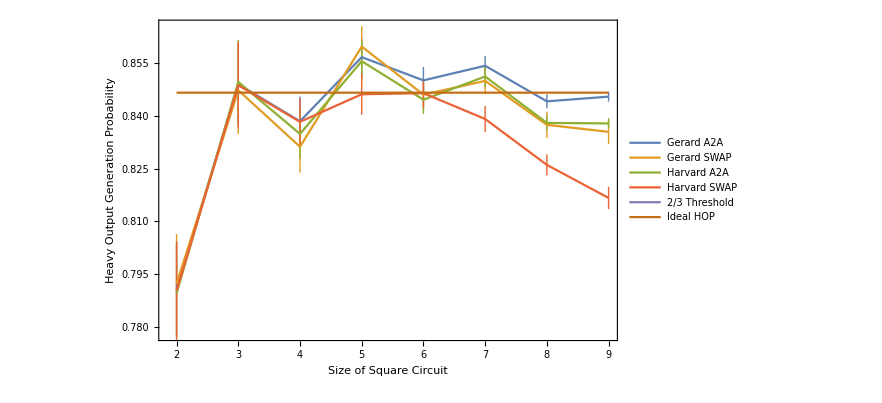

```mathematica
IdealHOP=Table[{i,(1+Log[2])/2},{i,2,9}];
Thresh=Table[{i,2/3},{i,2,9}];
ListPlot[{ErrorBars[GA2AQV[[All,1]]],ErrorBars[GSWAPQV[[All,1]]],ErrorBars[GMoveQV[[All,1]]],Thresh,IdealHOP},AxesLabel->{HoldForm[Layer Depth],HoldForm[Heavy Output  Probability]},Frame->True,FrameLabel->{"Size of Square Circuit","Mean Heavy Output Probability"},PlotMarkers->{Automatic,Automatic,Automatic,None,None},Joined->{False,False,False,True,True},PlotLegends->Placed[{"CZ_A All-to-All","CZ_A SWAP","CZ_B Movement","2/3 Threshold","Ideal HOP"},{Left,Bottom}]]
ListPlot[{ErrorBars[HA2AQV[[All,1]]],ErrorBars[HSWAPQV[[All,1]]],ErrorBars[HMoveQV[[All,1]]],Thresh,IdealHOP},AxesLabel->{HoldForm[Layer Depth],HoldForm[Heavy Output  Probability]},Frame->True,FrameLabel->{"Size of Square Circuit","Mean Heavy Output Probability"},PlotMarkers->{Automatic,Automatic,Automatic,None,None},Joined->{False,False,False,True,True},PlotLegends->Placed[{"CZ_B All-to-All","CZ_B SWAP","CZ_B Movement","2/3 Threshold","Ideal HOP"},{Left,Bottom}]]


ListPlot[{ErrorBars[GA2AQV[[All,2]]],ErrorBars[GSWAPQV[[All,2]]],ErrorBars[GMoveQV[[All,2]]],Thresh,IdealHOP},AxesLabel->{HoldForm[Layer Depth],HoldForm[Heavy Output Probability]},Frame->True,FrameLabel->{"Size of Square Circuit","Mean Heavy Output Probability"},PlotRange->All,PlotMarkers->{Automatic,Automatic,Automatic,None,None},Joined->{False,False,False,True,True},PlotLegends->Placed[{"CZ_A All-to-All","CZ_A SWAP","CZ_B Movement","2/3 Threshold","Ideal HOP"},{Right,Center}]]
ListPlot[{ErrorBars[HA2AQV[[All,2]]],ErrorBars[HSWAPQV[[All,2]]],ErrorBars[HMoveQV[[All,2]]],Thresh,IdealHOP},AxesLabel->{HoldForm[Layer Depth],HoldForm[Heavy Output Probability]},Frame->True,FrameLabel->{"Size of Square Circuit","Mean Heavy Output Probability"},PlotRange->All,PlotMarkers->{Automatic,Automatic,Automatic,None,None},Joined->{False,False,False,True,True},PlotLegends->Placed[{"CZ_B All-to-All","CZ_B SWAP","CZ_B Movement","2/3 Threshold","Ideal HOP"},{Right,Center}]]

ListPlot[{ErrorBarsLoss[GA2AQV[[All,3]]],ErrorBarsLoss[GSWAPQV[[All,3]]],ErrorBarsLoss[HA2AQV[[All,3]]],ErrorBarsLoss[HSWAPQV[[All,3]]]},AxesLabel->{HoldForm[Layer Depth],HoldForm[Heavy Output Probability]},Frame->True,FrameLabel->{"Size of Square Circuit","Mean Probability of Qubit Loss"},PlotRange->All,PlotMarkers->{Automatic,Small},IntervalMarkers->"Fences",PlotLegends->Placed[{"CZ_A All-to-All + Movement","CZ_A SWAP","CZ_B All-to-All + Movement","CZ_B SWAP"},{Left,Top}]]
```

```mathematica
PlusMinus[1]
```

±1